```mathematica
nBracket[n_]:=Table[i,{i,1,n}]
```

```mathematica
nBracket[5]
```

{1,2,3,4,5}

```mathematica
(*ToDo: Implement the Construction of all of the disctinct m-size lists from [n]*)
```

```mathematica
(*Proto-typical Combinatorial Recursion (the one I first implemented )*)
listRemove[list_,index_]:=
Module[
{
returnedList={},
lengthOfList=Length[list],
nope={}
},
For[
i=1,
i<lengthOfList+1,
i++,
If [
i!=index,
AppendTo[returnedList,list[[i]]]

]

];
returnedList
];


list ={};
sizeOfList=Null;
Recurse[source_,current_]:=
Module[
{
sourceAlpha=source,
currentAlpha=current,
iterator=1
},
{
While[
iterator<Length[source]+1, 

(*Print[iterator, Length[source]];*)
AppendTo[currentAlpha,source[[iterator]]];
Recurse[listRemove[sourceAlpha,iterator],currentAlpha];
currentAlpha = current;
iterator++

];

If[Length[currentAlpha]==sizeOfList,
AppendTo[list,currentAlpha];
];
}
];
```

```mathematica
listRemove[list_,index_]:=
Module[
{
returnedList={},
lengthOfList=Length[list],
nope={}
},
For[
i=1,
i<lengthOfList+1,
i++,
If [
i!=index,
AppendTo[returnedList,list[[i]]]

]

];
returnedList
];


list ={};
sizeOfList=Null;
listOmega:={0,1};
Recurse[current_]:=
Module[
{
currentAlpha=current,
iterator=1
},
{
If[Length[currentAlpha]==3,
{AppendTo[list,currentAlpha];
Print["foo"]
},
While[
iterator<Length[listOmega]+1, 

(*Print[iterator, Length[source]];*)
AppendTo[currentAlpha,listOmega[[iterator]]];
Recurse[currentAlpha];
currentAlpha = current;
iterator++
];
];
}
];
```

```mathematica
Recurse[{}]
```

foo

foo

foo

«5 more identical outputs»

{Null}

```mathematica
list
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
(*
ToDo: Comment on the below code, in particular, The If Statement above the While loop.
Andm comment on the structure of the Module;
	and, there's a link between this counting scheme, and the counting scheme for n!; derscribe it; describe how they are related..
*)
mArrangeN[listM_,sizeOfN_]:=Module[
{list :={},
listOmega:=listM
},
{
Recurse[current_]:=
Module[
{
currentAlpha=current,
iterator=1
},
{
(*Print[sizeOfN];*)
If[Length[currentAlpha]==sizeOfN,
{AppendTo[list,currentAlpha]
},
While[
iterator<Length[listOmega]+1, 

(*Print[iterator, Length[source]];*)
AppendTo[currentAlpha,listOmega[[iterator]]];
Recurse[currentAlpha];
currentAlpha = current;
iterator++
];
];
}
];

Recurse[{}];
list
}
]
```

```mathematica
result= mArrangeN[{0,1,2,3},3]
```

{{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,2,0},{0,2,1},{0,2,2},{0,2,3},{0,3,0},{0,3,1},{0,3,2},{0,3,3},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{2,0,0},{2,0,1},{2,0,2},{2,0,3},{2,1,0},{2,1,1},{2,1,2},{2,1,3},{2,2,0},{2,2,1},{2,2,2},{2,2,3},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{3,0,0},{3,0,1},{3,0,2},{3,0,3},{3,1,0},{3,1,1},{3,1,2},{3,1,3},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,3,0},{3,3,1},{3,3,2},{3,3,3}}}

```mathematica
list
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

```mathematica
result
```

{{{0,0,0},{0,0,1},{0,0,2},{0,0,3},{0,1,0},{0,1,1},{0,1,2},{0,1,3},{0,2,0},{0,2,1},{0,2,2},{0,2,3},{0,3,0},{0,3,1},{0,3,2},{0,3,3},{1,0,0},{1,0,1},{1,0,2},{1,0,3},{1,1,0},{1,1,1},{1,1,2},{1,1,3},{1,2,0},{1,2,1},{1,2,2},{1,2,3},{1,3,0},{1,3,1},{1,3,2},{1,3,3},{2,0,0},{2,0,1},{2,0,2},{2,0,3},{2,1,0},{2,1,1},{2,1,2},{2,1,3},{2,2,0},{2,2,1},{2,2,2},{2,2,3},{2,3,0},{2,3,1},{2,3,2},{2,3,3},{3,0,0},{3,0,1},{3,0,2},{3,0,3},{3,1,0},{3,1,1},{3,1,2},{3,1,3},{3,2,0},{3,2,1},{3,2,2},{3,2,3},{3,3,0},{3,3,1},{3,3,2},{3,3,3}}}

```mathematica
Length@result[[1]]
```

64

```mathematica
(*
Implement Cartesian Product
Note, recursion is useful for when the size of the lists are given ad hoc; aka when you don't know the size of lists a priori.

*)

CartesianProduct[listM_,listN_]:=Module[
{list :={},
listOmega:=listM,
listOmega2:= listN
},
{
generateListsOfPairs[current_]:=
Module[
{
currentAlpha=current,
iterator=1,
iteratorb=1

},
{
(*Print[sizeOfN];*)

While[
iterator<Length[listOmega]+1, 
(*Reset inner iterator*)
iteratorb=1;
While[
iteratorb<Length[listOmega2]+1,
AppendTo[list,{listOmega[[iterator]],listOmega2[[iteratorb]]}];
iteratorb++
];
iterator++
];

}
];

generateListsOfPairs[{}];
list
}
]

CartesianProduct[{0,1,2,3,4},{0,2,3}]
```

```mathematica
nBracket[n_]:=Table[i,{i,1,n}]
(*Permutations are bijective maps from nBracket, to nBracket*)
binaryNTuples[n_]:= mArrangeN[{0,1},n]
```

```mathematica
binaryNTuples[5]
```

{{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}}

```mathematica
CartesianProduct[{0,1,2,3,4},{0,2,3}]
```

{0,0}

{0,2}

{0,3}

{1,0}

{1,2}

{1,3}

{2,0}

{2,2}

{2,3}

{3,0}

{3,2}

{3,3}

{4,0}

{4,2}

{4,3}

{{{0,0},{0,2},{0,3},{1,0},{1,2},{1,3},{2,0},{2,2},{2,3},{3,0},{3,2},{3,3},{4,0},{4,2},{4,3}}}

{0,0}

{0,1}

{0,2}

{0,3}

{0,4}

{1,0}

{1,1}

{1,2}

{1,3}

{1,4}

{2,0}

{2,1}

{2,2}

{2,3}

{2,4}

{3,0}

{3,1}

{3,2}

{3,3}

{3,4}

{4,0}

{4,1}

{4,2}

{4,3}

{0,0}

{0,1}

{0,2}

{1,0}

{1,1}

{1,2}

{2,0}

{2,1}

{2,2}

{3,0}

{3,1}

{3,2}

{4,0}

{4,1}

{4,2}

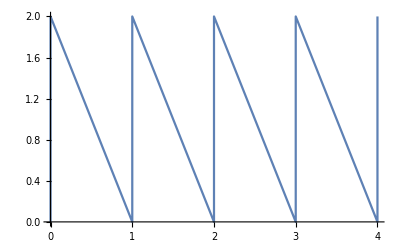

{0,0}

{0,1}

{0,2}

{0,3}

{0,4}

{1,0}

{1,1}

{1,2}

{1,3}

{1,4}

{2,0}

{2,1}

{2,2}

{2,3}

{2,4}

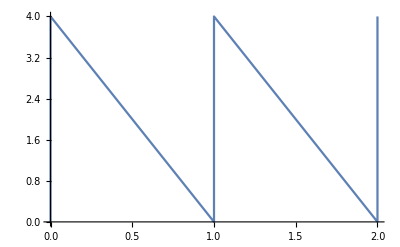

{0,0}

{0,1}

{0,2}

{0,3}

{0,4}

{1,0}

{1,1}

{1,2}

{1,3}

{1,4}

{2,0}

{2,1}

{2,2}

{2,3}

{2,4}

{3,0}

{3,1}

{3,2}

{3,3}

{3,4}

{4,0}

{4,1}

{4,2}

{4,3}

{4,4}

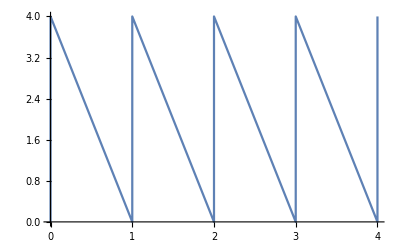

{4,4}
(*Why do I keep wanting to see the Catalan Paths in these plots? What does that list of ordered pairs look like?*)

-Graphics-

```mathematica
ListLinePlot@CartesianProduct[{0,1,2,3,4},{0,1,2}]
ListLinePlot@CartesianProduct[{0,1,2},{0,1,2,3,4}]
ListLinePlot@CartesianProduct[{0,1,2,3,4},{0,1,2,3,4}]
```

```mathematica
(*
TODO: Implement Equivalence Class Generator.
Given an Ad-hoc defined equivalence relation,
	return all pairs of elements which satisfy the relation.
First task: Find a way to define a relation, with some object/function (e.g. 1 < 3; x < y )
	give it to a function as input, to generate the set.

Compute the cartesian product of two given sets. 
Then, thread the function over the lists.

Turn on some boxes with lists?????????????

 
*)
```

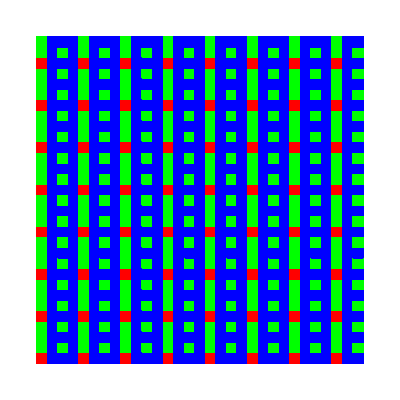

```mathematica
PadicNorm[x_Integer,p_Integer?PrimeQ]:=p^(-IntegerExponent[x,p])
PadicNorm[x_Rational,p_Integer?PrimeQ]:=PadicNorm[Numerator[x],p]/PadicNorm[Denominator[x],p]
v[x_]:=PadicNorm[x,2]
Graphics[{Table[{Which[v[k/30]>=v[n/30]&&v[k/30]>=1,Blue,v[k/30]<v[n/30]&&v[n/30]>=1,Green,v[k/30]<1&&v[n/30]<1,Red],Rectangle[{k/30,n/30},{(k+1)/30,(n+1)/30}]},{k,0,30},{n,0,30}]}]
```

```mathematica
TestListForRectangles :=CartesianProduct[{0,1,2,3,4},{0,1,2,3,4}];
(*TestListForRectangles[[1]]*)
(*Map[Rectangle[],TestListForRectangles[[1]]]*)
TestListForRectangles[[1,1]]
(*listFoo:=Table[TestListForRectangles[[1,i]],{i,1,Length@TestListForRectangles[[1]]}]*)
```

0

```mathematica
(*ArrayPlot@listFoo
Graphics@Map[Rectangle[Green,@],listFoo]*)


rectangles:=Table[{Red,Rectangle[TestListForRectangles[[1,i]]]},{i,1,Length@TestListForRectangles[[1]]}]
(*AppendTo[rectangles,{Red,Rectangle[{0,0}]}]*)
AppendTo[rectangles,{Green,Rectangle[{0,0}]}]

Graphics@rectangles
Show[Graphics[{Rectangle[{0,1}],Rectangle[{2,2}]}],Graphics@rectangles]
(*the pairs of integers are coordinates for where the rectangle will be in the grid.*)
```

{{RGBColor[1, 0, 0],Rectangle[0]},{RGBColor[1, 0, 0],Rectangle[1]},{RGBColor[1, 0, 0],Rectangle[2]},{RGBColor[1, 0, 0],Rectangle[3]},{RGBColor[1, 0, 0],Rectangle[4]},{RGBColor[0, 1, 0],Rectangle[{0,0}]}}

-Graphics-

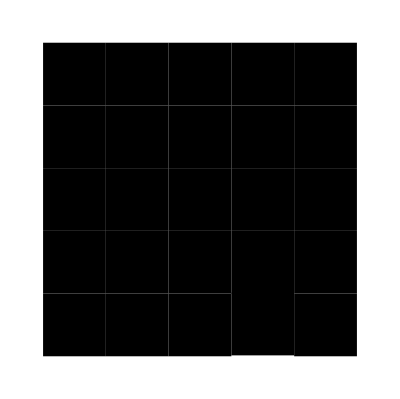

```mathematica
Graphics[Thick,Green,Rectangle[{0,1},{1,1}]]
```

-Graphics-

```mathematica
Show[Graphics[{Rectangle[{0,1}],Rectangle[{2,2}]}],Graphics@rectangles]
(*the pairs of integers are coordinates for where the rectangle will be in the grid.*)
```

-Graphics-